```mathematica
Get["cellzilla.m"]
```

cellzilla Version 1.3.0 (12 Nov 2008) using Mathematica Version 6.0 for Linux x86 (32-bit) (June 2, 2008) reloaded 12-November-2008 19:29:22.971495

Bruce Shapiro
12 Nov 2008
Annotated Example of Cellzilla for Wushel Model.

Ref: Activator Model of Jonsson et al (2005) Bioinformatics 21(S1):i232-i240
link to journal web site

The following is required to make the qhull library connect to Mathematica correctly in Linux.

```mathematica
$QHULL="";
```

## The stuff in this first section is what needs to be done by the program that is passing information to Cellzilla.

It will need to define the following (the names are unique to this example):

(1) centers - a list of {x,y} coordinates 
(2) theRateConstants - the list of rate constant values
(3) model - the cellerator model 
(4) diffusingSpecies - list of chemical species that diffuse and their associated rate constants
(5) theInitialConditions - list of initial conditions 

The information in (2) and (3) is identical in format to that produced by SME. 
The initial conditions in SME are different because they only correspond to a single cell.

### define the cell centers: this must be provided by the external program

```mathematica
centers={{34.8,55.68},{35.96,59.74},{36.54,51.04},{37.12,64.96},{38.28,62.06},{38.86,45.82},{38.86,50.46},{40.02,56.84},{40.6,66.12},{40.6,71.34},{41.18,48.72},{42.34,40.6},{42.34,53.94},{42.34,62.06},{42.92,92.8},{43.5,36.54},{44.08,57.42},{44.08,69.6},{44.08,80.62},{44.08,86.42},{44.08,99.76},{44.66,43.5},{44.66,59.74},{45.24,44.08},{45.24,48.14},{45.24,49.3},{45.82,65.54},{45.82,73.66},{46.4,97.44},{46.98,35.96},{46.98,68.44},{46.98,77.14},{47.56,64.38},{47.56,88.74},{47.56,94.54},{47.56,104.4},{48.14,43.5},{48.14,79.46},{48.72,50.46},{48.72,82.94},{48.72,89.32},{49.3,109.04},{49.88,38.28},{49.88,73.66},{50.46,63.8},{50.46,67.86},{50.46,102.08},{50.46,106.72},{51.04,100.92},{51.62,33.06},{51.62,85.84},{51.62,87.},{52.2,53.94},{52.2,59.16},{52.2,72.5},{52.2,80.62},{52.2,96.86},{52.2,111.94},{52.78,44.66},{52.78,92.22},{53.36,34.22},{53.94,80.04},{53.94,104.4},{54.52,37.7},{54.52,46.98},{54.52,75.4},{54.52,77.14},{55.1,68.44},{55.1,69.02},{55.68,52.78},{55.68,81.78},{55.68,88.16},{55.68,105.56},{56.26,58.},{56.26,64.96},{56.26,100.34},{56.26,109.62},{56.26,114.26},{56.84,78.3},{56.84,89.9},{56.84,96.86},{57.42,29.58},{57.42,39.44},{57.42,83.52},{57.42,95.12},{58.,73.08},{58.58,42.92},{58.58,93.96},{59.16,31.9},{59.16,62.06},{59.16,74.24},{59.16,106.72},{59.74,56.84},{59.74,68.44},{59.74,99.18},{60.32,33.64},{60.32,51.04},{60.32,70.18},{60.32,77.72},{61.48,44.66},{61.48,81.2},{61.48,88.16},{61.48,107.88},{62.06,52.78},{62.06,58.58},{62.06,72.5},{62.06,112.52},{62.64,64.96},{62.64,85.26},{62.64,91.06},{62.64,104.98},{63.8,93.38},{64.38,29.58},{64.38,44.66},{64.38,57.42},{64.38,63.22},{64.38,66.7},{64.38,75.4},{64.38,79.46},{64.38,98.02},{64.38,103.24},{64.38,115.42},{65.54,35.38},{65.54,49.3},{65.54,71.92},{65.54,99.18},{66.12,31.9},{66.12,52.78},{66.12,88.74},{66.7,53.94},{66.7,82.36},{67.86,40.6},{67.86,88.74},{68.44,30.74},{68.44,77.72},{68.44,107.88},{68.44,109.62},{69.02,100.34},{69.02,104.4},{69.6,50.46},{70.18,37.12},{70.18,58.58},{70.18,62.06},{70.18,91.64},{70.76,45.82},{70.76,58.},{70.76,78.88},{70.76,86.42},{70.76,95.7},{70.76,113.1},{71.34,62.06},{72.5,27.26},{72.5,31.32},{72.5,66.7},{72.5,75.4},{73.08,52.78},{73.08,104.98},{73.66,82.94},{73.66,106.14},{74.24,52.78},{74.24,58.},{74.24,70.76},{74.24,97.44},{74.82,39.44},{74.82,92.8},{75.4,65.54},{75.4,80.62},{75.4,86.42},{75.4,88.16},{75.4,101.5},{75.4,110.2},{75.98,29.58},{75.98,75.98},{76.56,80.04},{77.72,64.38},{78.3,35.96},{78.3,92.22},{78.88,26.68},{78.88,85.26},{78.88,97.44},{78.88,102.08},{78.88,107.88},{79.46,69.02},{79.46,73.08},{80.04,31.9},{80.04,55.1},{80.04,80.62},{80.62,49.3},{80.62,77.72},{81.2,58.58},{81.2,84.68},{81.2,88.16},{81.2,89.32},{81.2,92.8},{81.78,69.6},{81.78,99.76},{82.36,36.54},{82.36,53.94},{82.36,65.54},{82.36,104.98},{82.94,42.34},{82.94,75.4},{83.52,29.},{83.52,94.54},{85.26,81.2},{85.26,89.32},{85.84,62.64},{86.42,32.48},{86.42,38.28},{86.42,76.56},{86.42,100.92},{87.,63.8},{87.,72.5},{87.,96.86},{87.58,56.84},{87.58,85.26},{87.58,92.8},{88.16,46.4},{88.74,27.84},{89.32,42.34},{89.32,89.9},{89.9,69.02},{90.48,67.86},{90.48,71.34},{91.06,78.88},{91.64,33.64},{92.22,37.7},{92.22,48.72},{92.8,42.92},{93.38,62.06},{93.38,71.34},{93.96,58.},{94.54,56.84},{95.12,79.46},{95.7,53.36},{95.7,64.38},{96.28,31.9},{96.28,66.7},{96.86,37.12},{96.86,48.14},{97.44,53.94},{98.02,42.92},{98.02,49.88},{98.02,72.5},{99.18,60.32},{99.76,68.44},{100.34,48.72},{100.92,64.38},{101.5,35.96},{102.66,40.6},{102.66,55.68},{104.4,46.98},{104.4,52.78}};
```

### Define the model and the rate constants

```mathematica
theRateConstants={ky-> 0.2, dy-> 0.1, Dy-> 0.1, kD-> 3.0, tauw-> 10, dw-> 0.1, hw-> 0, Twy-> -20, Twa-> 0.5, a-> 0.1, b-> 0.2, beta-> 0.1, c-> 0.1, d-> 0.01, Da-> 0.1, Db-> 1.5};
```

```mathematica
model= {
{Y↦W,GRN[1/tauw,Twy,1,hw,sigma]},
{A↦W, GRN[1/tauw,Twa,1,hw,sigma]},
{W->∅, dw},
{L1->Y+L1, ky},
 {Y->∅, dy}, 
{A+Y-> Y, d},
 {∅⇄A, a, beta},
{2A+B->3A,c}, 
{A->B, b}
};
```

```mathematica
diffusingSpecies={{Y, Dy}, {A, Da}, {B, Db}};
```

### Figure out the initial Conditions

#### The following is used to figure out which cells are on the surface. This is because we need to have different initial conditions (for this specific model) on the surface

```mathematica
sc=surfaceLayer[centers]
```

{1,2,3,4,6,10,12,15,16,19,20,21,30,36,42,50,58,78,82,107,113,122,134,150,152,171,178,182,200,203,211,214,216,217,219,221,234,237,244,245,246,248,249,250,251,252,253}

```mathematica
n=Length[centers]; 
WIC=(W[#]-> 0)&/@Range[n];
YIC=(Y[#]-> 0)&/@Range[n];
AIC=(A[#]-> 0)&/@Range[n]; 
BIC=(B[#]-> 0)&/@Range[n]; 
L1IC=(L1[#]-> If[MemberQ[sc, #], 1, 0])&/@Range[n];
theInitialConditions=Join[WIC, YIC, AIC, BIC, L1IC]
```

{W[1]→0,W[2]→0,W[3]→0,W[4]→0,W[5]→0,W[6]→0,W[7]→0,W[8]→0,W[9]→0,W[10]→0,W[11]→0,W[12]→0,W[13]→0,W[14]→0,W[15]→0,W[16]→0,W[17]→0,W[18]→0,W[19]→0,W[20]→0,W[21]→0,W[22]→0,W[23]→0,W[24]→0,W[25]→0,W[26]→0,W[27]→0,W[28]→0,W[29]→0,W[30]→0,W[31]→0,W[32]→0,W[33]→0,W[34]→0,W[35]→0,W[36]→0,W[37]→0,W[38]→0,W[39]→0,W[40]→0,W[41]→0,W[42]→0,W[43]→0,W[44]→0,W[45]→0,W[46]→0,W[47]→0,W[48]→0,W[49]→0,W[50]→0,W[51]→0,W[52]→0,W[53]→0,W[54]→0,W[55]→0,W[56]→0,W[57]→0,W[58]→0,W[59]→0,W[60]→0,W[61]→0,W[62]→0,W[63]→0,W[64]→0,W[65]→0,W[66]→0,W[67]→0,W[68]→0,W[69]→0,W[70]→0,W[71]→0,W[72]→0,W[73]→0,W[74]→0,W[75]→0,W[76]→0,W[77]→0,W[78]→0,W[79]→0,W[80]→0,W[81]→0,W[82]→0,W[83]→0,W[84]→0,W[85]→0,W[86]→0,W[87]→0,W[88]→0,W[89]→0,W[90]→0,W[91]→0,W[92]→0,W[93]→0,W[94]→0,W[95]→0,W[96]→0,W[97]→0,W[98]→0,W[99]→0,W[100]→0,W[101]→0,W[102]→0,W[103]→0,W[104]→0,W[105]→0,W[106]→0,W[107]→0,W[108]→0,W[109]→0,W[110]→0,W[111]→0,W[112]→0,W[113]→0,W[114]→0,W[115]→0,W[116]→0,W[117]→0,W[118]→0,W[119]→0,W[120]→0,W[121]→0,W[122]→0,W[123]→0,W[124]→0,W[125]→0,W[126]→0,W[127]→0,W[128]→0,W[129]→0,W[130]→0,W[131]→0,W[132]→0,W[133]→0,W[134]→0,W[135]→0,W[136]→0,W[137]→0,W[138]→0,W[139]→0,W[140]→0,W[141]→0,W[142]→0,W[143]→0,W[144]→0,W[145]→0,W[146]→0,W[147]→0,W[148]→0,W[149]→0,W[150]→0,W[151]→0,W[152]→0,W[153]→0,W[154]→0,W[155]→0,W[156]→0,W[157]→0,W[158]→0,W[159]→0,W[160]→0,W[161]→0,W[162]→0,W[163]→0,W[164]→0,W[165]→0,W[166]→0,W[167]→0,W[168]→0,W[169]→0,W[170]→0,W[171]→0,W[172]→0,W[173]→0,W[174]→0,W[175]→0,W[176]→0,W[177]→0,W[178]→0,W[179]→0,W[180]→0,W[181]→0,W[182]→0,W[183]→0,W[184]→0,W[185]→0,W[186]→0,W[187]→0,W[188]→0,W[189]→0,W[190]→0,W[191]→0,W[192]→0,W[193]→0,W[194]→0,W[195]→0,W[196]→0,W[197]→0,W[198]→0,W[199]→0,W[200]→0,W[201]→0,W[202]→0,W[203]→0,W[204]→0,W[205]→0,W[206]→0,W[207]→0,W[208]→0,W[209]→0,W[210]→0,W[211]→0,W[212]→0,W[213]→0,W[214]→0,W[215]→0,W[216]→0,W[217]→0,W[218]→0,W[219]→0,W[220]→0,W[221]→0,W[222]→0,W[223]→0,W[224]→0,W[225]→0,W[226]→0,W[227]→0,W[228]→0,W[229]→0,W[230]→0,W[231]→0,W[232]→0,W[233]→0,W[234]→0,W[235]→0,W[236]→0,W[237]→0,W[238]→0,W[239]→0,W[240]→0,W[241]→0,W[242]→0,W[243]→0,W[244]→0,W[245]→0,W[246]→0,W[247]→0,W[248]→0,W[249]→0,W[250]→0,W[251]→0,W[252]→0,W[253]→0,Y[1]→0,Y[2]→0,Y[3]→0,Y[4]→0,Y[5]→0,Y[6]→0,Y[7]→0,Y[8]→0,Y[9]→0,Y[10]→0,Y[11]→0,Y[12]→0,Y[13]→0,Y[14]→0,Y[15]→0,Y[16]→0,Y[17]→0,Y[18]→0,Y[19]→0,Y[20]→0,Y[21]→0,Y[22]→0,Y[23]→0,Y[24]→0,Y[25]→0,Y[26]→0,Y[27]→0,Y[28]→0,Y[29]→0,Y[30]→0,Y[31]→0,Y[32]→0,Y[33]→0,Y[34]→0,Y[35]→0,Y[36]→0,Y[37]→0,Y[38]→0,Y[39]→0,Y[40]→0,Y[41]→0,Y[42]→0,Y[43]→0,Y[44]→0,Y[45]→0,Y[46]→0,Y[47]→0,Y[48]→0,Y[49]→0,Y[50]→0,Y[51]→0,Y[52]→0,Y[53]→0,Y[54]→0,Y[55]→0,Y[56]→0,Y[57]→0,Y[58]→0,Y[59]→0,Y[60]→0,Y[61]→0,Y[62]→0,Y[63]→0,Y[64]→0,Y[65]→0,Y[66]→0,Y[67]→0,Y[68]→0,Y[69]→0,Y[70]→0,Y[71]→0,Y[72]→0,Y[73]→0,Y[74]→0,Y[75]→0,Y[76]→0,Y[77]→0,Y[78]→0,Y[79]→0,Y[80]→0,Y[81]→0,Y[82]→0,Y[83]→0,Y[84]→0,Y[85]→0,Y[86]→0,Y[87]→0,Y[88]→0,Y[89]→0,Y[90]→0,Y[91]→0,Y[92]→0,Y[93]→0,Y[94]→0,Y[95]→0,Y[96]→0,Y[97]→0,Y[98]→0,Y[99]→0,Y[100]→0,Y[101]→0,Y[102]→0,Y[103]→0,Y[104]→0,Y[105]→0,Y[106]→0,Y[107]→0,Y[108]→0,Y[109]→0,Y[110]→0,Y[111]→0,Y[112]→0,Y[113]→0,Y[114]→0,Y[115]→0,Y[116]→0,Y[117]→0,Y[118]→0,Y[119]→0,Y[120]→0,Y[121]→0,Y[122]→0,Y[123]→0,Y[124]→0,Y[125]→0,Y[126]→0,Y[127]→0,Y[128]→0,Y[129]→0,Y[130]→0,Y[131]→0,Y[132]→0,Y[133]→0,Y[134]→0,Y[135]→0,Y[136]→0,Y[137]→0,Y[138]→0,Y[139]→0,Y[140]→0,Y[141]→0,Y[142]→0,Y[143]→0,Y[144]→0,Y[145]→0,Y[146]→0,Y[147]→0,Y[148]→0,Y[149]→0,Y[150]→0,Y[151]→0,Y[152]→0,Y[153]→0,Y[154]→0,Y[155]→0,Y[156]→0,Y[157]→0,Y[158]→0,Y[159]→0,Y[160]→0,Y[161]→0,Y[162]→0,Y[163]→0,Y[164]→0,Y[165]→0,Y[166]→0,Y[167]→0,Y[168]→0,Y[169]→0,Y[170]→0,Y[171]→0,Y[172]→0,Y[173]→0,Y[174]→0,Y[175]→0,Y[176]→0,Y[177]→0,Y[178]→0,Y[179]→0,Y[180]→0,Y[181]→0,Y[182]→0,Y[183]→0,Y[184]→0,Y[185]→0,Y[186]→0,Y[187]→0,Y[188]→0,Y[189]→0,Y[190]→0,Y[191]→0,Y[192]→0,Y[193]→0,Y[194]→0,Y[195]→0,Y[196]→0,Y[197]→0,Y[198]→0,Y[199]→0,Y[200]→0,Y[201]→0,Y[202]→0,Y[203]→0,Y[204]→0,Y[205]→0,Y[206]→0,Y[207]→0,Y[208]→0,Y[209]→0,Y[210]→0,Y[211]→0,Y[212]→0,Y[213]→0,Y[214]→0,Y[215]→0,Y[216]→0,Y[217]→0,Y[218]→0,Y[219]→0,Y[220]→0,Y[221]→0,Y[222]→0,Y[223]→0,Y[224]→0,Y[225]→0,Y[226]→0,Y[227]→0,Y[228]→0,Y[229]→0,Y[230]→0,Y[231]→0,Y[232]→0,Y[233]→0,Y[234]→0,Y[235]→0,Y[236]→0,Y[237]→0,Y[238]→0,Y[239]→0,Y[240]→0,Y[241]→0,Y[242]→0,Y[243]→0,Y[244]→0,Y[245]→0,Y[246]→0,Y[247]→0,Y[248]→0,Y[249]→0,Y[250]→0,Y[251]→0,Y[252]→0,Y[253]→0,A[1]→0,A[2]→0,A[3]→0,A[4]→0,A[5]→0,A[6]→0,A[7]→0,A[8]→0,A[9]→0,A[10]→0,A[11]→0,A[12]→0,A[13]→0,A[14]→0,A[15]→0,A[16]→0,A[17]→0,A[18]→0,A[19]→0,A[20]→0,A[21]→0,A[22]→0,A[23]→0,A[24]→0,A[25]→0,A[26]→0,A[27]→0,A[28]→0,A[29]→0,A[30]→0,A[31]→0,A[32]→0,A[33]→0,A[34]→0,A[35]→0,A[36]→0,A[37]→0,A[38]→0,A[39]→0,A[40]→0,A[41]→0,A[42]→0,A[43]→0,A[44]→0,A[45]→0,A[46]→0,A[47]→0,A[48]→0,A[49]→0,A[50]→0,A[51]→0,A[52]→0,A[53]→0,A[54]→0,A[55]→0,A[56]→0,A[57]→0,A[58]→0,A[59]→0,A[60]→0,A[61]→0,A[62]→0,A[63]→0,A[64]→0,A[65]→0,A[66]→0,A[67]→0,A[68]→0,A[69]→0,A[70]→0,A[71]→0,A[72]→0,A[73]→0,A[74]→0,A[75]→0,A[76]→0,A[77]→0,A[78]→0,A[79]→0,A[80]→0,A[81]→0,A[82]→0,A[83]→0,A[84]→0,A[85]→0,A[86]→0,A[87]→0,A[88]→0,A[89]→0,A[90]→0,A[91]→0,A[92]→0,A[93]→0,A[94]→0,A[95]→0,A[96]→0,A[97]→0,A[98]→0,A[99]→0,A[100]→0,A[101]→0,A[102]→0,A[103]→0,A[104]→0,A[105]→0,A[106]→0,A[107]→0,A[108]→0,A[109]→0,A[110]→0,A[111]→0,A[112]→0,A[113]→0,A[114]→0,A[115]→0,A[116]→0,A[117]→0,A[118]→0,A[119]→0,A[120]→0,A[121]→0,A[122]→0,A[123]→0,A[124]→0,A[125]→0,A[126]→0,A[127]→0,A[128]→0,A[129]→0,A[130]→0,A[131]→0,A[132]→0,A[133]→0,A[134]→0,A[135]→0,A[136]→0,A[137]→0,A[138]→0,A[139]→0,A[140]→0,A[141]→0,A[142]→0,A[143]→0,A[144]→0,A[145]→0,A[146]→0,A[147]→0,A[148]→0,A[149]→0,A[150]→0,A[151]→0,A[152]→0,A[153]→0,A[154]→0,A[155]→0,A[156]→0,A[157]→0,A[158]→0,A[159]→0,A[160]→0,A[161]→0,A[162]→0,A[163]→0,A[164]→0,A[165]→0,A[166]→0,A[167]→0,A[168]→0,A[169]→0,A[170]→0,A[171]→0,A[172]→0,A[173]→0,A[174]→0,A[175]→0,A[176]→0,A[177]→0,A[178]→0,A[179]→0,A[180]→0,A[181]→0,A[182]→0,A[183]→0,A[184]→0,A[185]→0,A[186]→0,A[187]→0,A[188]→0,A[189]→0,A[190]→0,A[191]→0,A[192]→0,A[193]→0,A[194]→0,A[195]→0,A[196]→0,A[197]→0,A[198]→0,A[199]→0,A[200]→0,A[201]→0,A[202]→0,A[203]→0,A[204]→0,A[205]→0,A[206]→0,A[207]→0,A[208]→0,A[209]→0,A[210]→0,A[211]→0,A[212]→0,A[213]→0,A[214]→0,A[215]→0,A[216]→0,A[217]→0,A[218]→0,A[219]→0,A[220]→0,A[221]→0,A[222]→0,A[223]→0,A[224]→0,A[225]→0,A[226]→0,A[227]→0,A[228]→0,A[229]→0,A[230]→0,A[231]→0,A[232]→0,A[233]→0,A[234]→0,A[235]→0,A[236]→0,A[237]→0,A[238]→0,A[239]→0,A[240]→0,A[241]→0,A[242]→0,A[243]→0,A[244]→0,A[245]→0,A[246]→0,A[247]→0,A[248]→0,A[249]→0,A[250]→0,A[251]→0,A[252]→0,A[253]→0,B[1]→0,B[2]→0,B[3]→0,B[4]→0,B[5]→0,B[6]→0,B[7]→0,B[8]→0,B[9]→0,B[10]→0,B[11]→0,B[12]→0,B[13]→0,B[14]→0,B[15]→0,B[16]→0,B[17]→0,B[18]→0,B[19]→0,B[20]→0,B[21]→0,B[22]→0,B[23]→0,B[24]→0,B[25]→0,B[26]→0,B[27]→0,B[28]→0,B[29]→0,B[30]→0,B[31]→0,B[32]→0,B[33]→0,B[34]→0,B[35]→0,B[36]→0,B[37]→0,B[38]→0,B[39]→0,B[40]→0,B[41]→0,B[42]→0,B[43]→0,B[44]→0,B[45]→0,B[46]→0,B[47]→0,B[48]→0,B[49]→0,B[50]→0,B[51]→0,B[52]→0,B[53]→0,B[54]→0,B[55]→0,B[56]→0,B[57]→0,B[58]→0,B[59]→0,B[60]→0,B[61]→0,B[62]→0,B[63]→0,B[64]→0,B[65]→0,B[66]→0,B[67]→0,B[68]→0,B[69]→0,B[70]→0,B[71]→0,B[72]→0,B[73]→0,B[74]→0,B[75]→0,B[76]→0,B[77]→0,B[78]→0,B[79]→0,B[80]→0,B[81]→0,B[82]→0,B[83]→0,B[84]→0,B[85]→0,B[86]→0,B[87]→0,B[88]→0,B[89]→0,B[90]→0,B[91]→0,B[92]→0,B[93]→0,B[94]→0,B[95]→0,B[96]→0,B[97]→0,B[98]→0,B[99]→0,B[100]→0,B[101]→0,B[102]→0,B[103]→0,B[104]→0,B[105]→0,B[106]→0,B[107]→0,B[108]→0,B[109]→0,B[110]→0,B[111]→0,B[112]→0,B[113]→0,B[114]→0,B[115]→0,B[116]→0,B[117]→0,B[118]→0,B[119]→0,B[120]→0,B[121]→0,B[122]→0,B[123]→0,B[124]→0,B[125]→0,B[126]→0,B[127]→0,B[128]→0,B[129]→0,B[130]→0,B[131]→0,B[132]→0,B[133]→0,B[134]→0,B[135]→0,B[136]→0,B[137]→0,B[138]→0,B[139]→0,B[140]→0,B[141]→0,B[142]→0,B[143]→0,B[144]→0,B[145]→0,B[146]→0,B[147]→0,B[148]→0,B[149]→0,B[150]→0,B[151]→0,B[152]→0,B[153]→0,B[154]→0,B[155]→0,B[156]→0,B[157]→0,B[158]→0,B[159]→0,B[160]→0,B[161]→0,B[162]→0,B[163]→0,B[164]→0,B[165]→0,B[166]→0,B[167]→0,B[168]→0,B[169]→0,B[170]→0,B[171]→0,B[172]→0,B[173]→0,B[174]→0,B[175]→0,B[176]→0,B[177]→0,B[178]→0,B[179]→0,B[180]→0,B[181]→0,B[182]→0,B[183]→0,B[184]→0,B[185]→0,B[186]→0,B[187]→0,B[188]→0,B[189]→0,B[190]→0,B[191]→0,B[192]→0,B[193]→0,B[194]→0,B[195]→0,B[196]→0,B[197]→0,B[198]→0,B[199]→0,B[200]→0,B[201]→0,B[202]→0,B[203]→0,B[204]→0,B[205]→0,B[206]→0,B[207]→0,B[208]→0,B[209]→0,B[210]→0,B[211]→0,B[212]→0,B[213]→0,B[214]→0,B[215]→0,B[216]→0,B[217]→0,B[218]→0,B[219]→0,B[220]→0,B[221]→0,B[222]→0,B[223]→0,B[224]→0,B[225]→0,B[226]→0,B[227]→0,B[228]→0,B[229]→0,B[230]→0,B[231]→0,B[232]→0,B[233]→0,B[234]→0,B[235]→0,B[236]→0,B[237]→0,B[238]→0,B[239]→0,B[240]→0,B[241]→0,B[242]→0,B[243]→0,B[244]→0,B[245]→0,B[246]→0,B[247]→0,B[248]→0,B[249]→0,B[250]→0,B[251]→0,B[252]→0,B[253]→0,L1[1]→1,L1[2]→1,L1[3]→1,L1[4]→1,L1[5]→0,L1[6]→1,L1[7]→0,L1[8]→0,L1[9]→0,L1[10]→1,L1[11]→0,L1[12]→1,L1[13]→0,L1[14]→0,L1[15]→1,L1[16]→1,L1[17]→0,L1[18]→0,L1[19]→1,L1[20]→1,L1[21]→1,L1[22]→0,L1[23]→0,L1[24]→0,L1[25]→0,L1[26]→0,L1[27]→0,L1[28]→0,L1[29]→0,L1[30]→1,L1[31]→0,L1[32]→0,L1[33]→0,L1[34]→0,L1[35]→0,L1[36]→1,L1[37]→0,L1[38]→0,L1[39]→0,L1[40]→0,L1[41]→0,L1[42]→1,L1[43]→0,L1[44]→0,L1[45]→0,L1[46]→0,L1[47]→0,L1[48]→0,L1[49]→0,L1[50]→1,L1[51]→0,L1[52]→0,L1[53]→0,L1[54]→0,L1[55]→0,L1[56]→0,L1[57]→0,L1[58]→1,L1[59]→0,L1[60]→0,L1[61]→0,L1[62]→0,L1[63]→0,L1[64]→0,L1[65]→0,L1[66]→0,L1[67]→0,L1[68]→0,L1[69]→0,L1[70]→0,L1[71]→0,L1[72]→0,L1[73]→0,L1[74]→0,L1[75]→0,L1[76]→0,L1[77]→0,L1[78]→1,L1[79]→0,L1[80]→0,L1[81]→0,L1[82]→1,L1[83]→0,L1[84]→0,L1[85]→0,L1[86]→0,L1[87]→0,L1[88]→0,L1[89]→0,L1[90]→0,L1[91]→0,L1[92]→0,L1[93]→0,L1[94]→0,L1[95]→0,L1[96]→0,L1[97]→0,L1[98]→0,L1[99]→0,L1[100]→0,L1[101]→0,L1[102]→0,L1[103]→0,L1[104]→0,L1[105]→0,L1[106]→0,L1[107]→1,L1[108]→0,L1[109]→0,L1[110]→0,L1[111]→0,L1[112]→0,L1[113]→1,L1[114]→0,L1[115]→0,L1[116]→0,L1[117]→0,L1[118]→0,L1[119]→0,L1[120]→0,L1[121]→0,L1[122]→1,L1[123]→0,L1[124]→0,L1[125]→0,L1[126]→0,L1[127]→0,L1[128]→0,L1[129]→0,L1[130]→0,L1[131]→0,L1[132]→0,L1[133]→0,L1[134]→1,L1[135]→0,L1[136]→0,L1[137]→0,L1[138]→0,L1[139]→0,L1[140]→0,L1[141]→0,L1[142]→0,L1[143]→0,L1[144]→0,L1[145]→0,L1[146]→0,L1[147]→0,L1[148]→0,L1[149]→0,L1[150]→1,L1[151]→0,L1[152]→1,L1[153]→0,L1[154]→0,L1[155]→0,L1[156]→0,L1[157]→0,L1[158]→0,L1[159]→0,L1[160]→0,L1[161]→0,L1[162]→0,L1[163]→0,L1[164]→0,L1[165]→0,L1[166]→0,L1[167]→0,L1[168]→0,L1[169]→0,L1[170]→0,L1[171]→1,L1[172]→0,L1[173]→0,L1[174]→0,L1[175]→0,L1[176]→0,L1[177]→0,L1[178]→1,L1[179]→0,L1[180]→0,L1[181]→0,L1[182]→1,L1[183]→0,L1[184]→0,L1[185]→0,L1[186]→0,L1[187]→0,L1[188]→0,L1[189]→0,L1[190]→0,L1[191]→0,L1[192]→0,L1[193]→0,L1[194]→0,L1[195]→0,L1[196]→0,L1[197]→0,L1[198]→0,L1[199]→0,L1[200]→1,L1[201]→0,L1[202]→0,L1[203]→1,L1[204]→0,L1[205]→0,L1[206]→0,L1[207]→0,L1[208]→0,L1[209]→0,L1[210]→0,L1[211]→1,L1[212]→0,L1[213]→0,L1[214]→1,L1[215]→0,L1[216]→1,L1[217]→1,L1[218]→0,L1[219]→1,L1[220]→0,L1[221]→1,L1[222]→0,L1[223]→0,L1[224]→0,L1[225]→0,L1[226]→0,L1[227]→0,L1[228]→0,L1[229]→0,L1[230]→0,L1[231]→0,L1[232]→0,L1[233]→0,L1[234]→1,L1[235]→0,L1[236]→0,L1[237]→1,L1[238]→0,L1[239]→0,L1[240]→0,L1[241]→0,L1[242]→0,L1[243]→0,L1[244]→1,L1[245]→1,L1[246]→1,L1[247]→0,L1[248]→1,L1[249]→1,L1[250]→1,L1[251]→1,L1[252]→1,L1[253]→1}

## This is where Cellzilla would begin

### First we list the required output. In this particular notebook this listing is optional, it is just for explanatory purposes.

```mathematica
centers
```

{{34.8,55.68},{35.96,59.74},{36.54,51.04},{37.12,64.96},{38.28,62.06},{38.86,45.82},{38.86,50.46},{40.02,56.84},{40.6,66.12},{40.6,71.34},{41.18,48.72},{42.34,40.6},{42.34,53.94},{42.34,62.06},{42.92,92.8},{43.5,36.54},{44.08,57.42},{44.08,69.6},{44.08,80.62},{44.08,86.42},{44.08,99.76},{44.66,43.5},{44.66,59.74},{45.24,44.08},{45.24,48.14},{45.24,49.3},{45.82,65.54},{45.82,73.66},{46.4,97.44},{46.98,35.96},{46.98,68.44},{46.98,77.14},{47.56,64.38},{47.56,88.74},{47.56,94.54},{47.56,104.4},{48.14,43.5},{48.14,79.46},{48.72,50.46},{48.72,82.94},{48.72,89.32},{49.3,109.04},{49.88,38.28},{49.88,73.66},{50.46,63.8},{50.46,67.86},{50.46,102.08},{50.46,106.72},{51.04,100.92},{51.62,33.06},{51.62,85.84},{51.62,87.},{52.2,53.94},{52.2,59.16},{52.2,72.5},{52.2,80.62},{52.2,96.86},{52.2,111.94},{52.78,44.66},{52.78,92.22},{53.36,34.22},{53.94,80.04},{53.94,104.4},{54.52,37.7},{54.52,46.98},{54.52,75.4},{54.52,77.14},{55.1,68.44},{55.1,69.02},{55.68,52.78},{55.68,81.78},{55.68,88.16},{55.68,105.56},{56.26,58.},{56.26,64.96},{56.26,100.34},{56.26,109.62},{56.26,114.26},{56.84,78.3},{56.84,89.9},{56.84,96.86},{57.42,29.58},{57.42,39.44},{57.42,83.52},{57.42,95.12},{58.,73.08},{58.58,42.92},{58.58,93.96},{59.16,31.9},{59.16,62.06},{59.16,74.24},{59.16,106.72},{59.74,56.84},{59.74,68.44},{59.74,99.18},{60.32,33.64},{60.32,51.04},{60.32,70.18},{60.32,77.72},{61.48,44.66},{61.48,81.2},{61.48,88.16},{61.48,107.88},{62.06,52.78},{62.06,58.58},{62.06,72.5},{62.06,112.52},{62.64,64.96},{62.64,85.26},{62.64,91.06},{62.64,104.98},{63.8,93.38},{64.38,29.58},{64.38,44.66},{64.38,57.42},{64.38,63.22},{64.38,66.7},{64.38,75.4},{64.38,79.46},{64.38,98.02},{64.38,103.24},{64.38,115.42},{65.54,35.38},{65.54,49.3},{65.54,71.92},{65.54,99.18},{66.12,31.9},{66.12,52.78},{66.12,88.74},{66.7,53.94},{66.7,82.36},{67.86,40.6},{67.86,88.74},{68.44,30.74},{68.44,77.72},{68.44,107.88},{68.44,109.62},{69.02,100.34},{69.02,104.4},{69.6,50.46},{70.18,37.12},{70.18,58.58},{70.18,62.06},{70.18,91.64},{70.76,45.82},{70.76,58.},{70.76,78.88},{70.76,86.42},{70.76,95.7},{70.76,113.1},{71.34,62.06},{72.5,27.26},{72.5,31.32},{72.5,66.7},{72.5,75.4},{73.08,52.78},{73.08,104.98},{73.66,82.94},{73.66,106.14},{74.24,52.78},{74.24,58.},{74.24,70.76},{74.24,97.44},{74.82,39.44},{74.82,92.8},{75.4,65.54},{75.4,80.62},{75.4,86.42},{75.4,88.16},{75.4,101.5},{75.4,110.2},{75.98,29.58},{75.98,75.98},{76.56,80.04},{77.72,64.38},{78.3,35.96},{78.3,92.22},{78.88,26.68},{78.88,85.26},{78.88,97.44},{78.88,102.08},{78.88,107.88},{79.46,69.02},{79.46,73.08},{80.04,31.9},{80.04,55.1},{80.04,80.62},{80.62,49.3},{80.62,77.72},{81.2,58.58},{81.2,84.68},{81.2,88.16},{81.2,89.32},{81.2,92.8},{81.78,69.6},{81.78,99.76},{82.36,36.54},{82.36,53.94},{82.36,65.54},{82.36,104.98},{82.94,42.34},{82.94,75.4},{83.52,29.},{83.52,94.54},{85.26,81.2},{85.26,89.32},{85.84,62.64},{86.42,32.48},{86.42,38.28},{86.42,76.56},{86.42,100.92},{87.,63.8},{87.,72.5},{87.,96.86},{87.58,56.84},{87.58,85.26},{87.58,92.8},{88.16,46.4},{88.74,27.84},{89.32,42.34},{89.32,89.9},{89.9,69.02},{90.48,67.86},{90.48,71.34},{91.06,78.88},{91.64,33.64},{92.22,37.7},{92.22,48.72},{92.8,42.92},{93.38,62.06},{93.38,71.34},{93.96,58.},{94.54,56.84},{95.12,79.46},{95.7,53.36},{95.7,64.38},{96.28,31.9},{96.28,66.7},{96.86,37.12},{96.86,48.14},{97.44,53.94},{98.02,42.92},{98.02,49.88},{98.02,72.5},{99.18,60.32},{99.76,68.44},{100.34,48.72},{100.92,64.38},{101.5,35.96},{102.66,40.6},{102.66,55.68},{104.4,46.98},{104.4,52.78}}

```mathematica
theRateConstants
```

{ky→0.2,dy→0.1,Dy→0.1,kD→3.,tauw→10,dw→0.1,hw→0,Twy→-20,Twa→0.5,a→0.1,b→0.2,beta→0.1,c→0.1,d→0.01,Da→0.1,Db→1.5}

```mathematica
model
```

{{Y↦W,GRN[1/tauw,Twy,1,hw,sigma]},{A↦W,GRN[1/tauw,Twa,1,hw,sigma]},{W→∅,dw},{L1→L1+Y,ky},{Y→∅,dy},{A+Y→Y,d},{∅⇄A,a,beta},{2 A+B→3 A,c},{A→B,b}}

```mathematica
diffusingSpecies
```

{{Y,Dy},{A,Da},{B,Db}}

```mathematica
theInitialConditions
```

{W[1]→0,W[2]→0,W[3]→0,W[4]→0,W[5]→0,W[6]→0,W[7]→0,W[8]→0,W[9]→0,W[10]→0,W[11]→0,W[12]→0,W[13]→0,W[14]→0,W[15]→0,W[16]→0,W[17]→0,W[18]→0,W[19]→0,W[20]→0,W[21]→0,W[22]→0,W[23]→0,W[24]→0,W[25]→0,W[26]→0,W[27]→0,W[28]→0,W[29]→0,W[30]→0,W[31]→0,W[32]→0,W[33]→0,W[34]→0,W[35]→0,W[36]→0,W[37]→0,W[38]→0,W[39]→0,W[40]→0,W[41]→0,W[42]→0,W[43]→0,W[44]→0,W[45]→0,W[46]→0,W[47]→0,W[48]→0,W[49]→0,W[50]→0,W[51]→0,W[52]→0,W[53]→0,W[54]→0,W[55]→0,W[56]→0,W[57]→0,W[58]→0,W[59]→0,W[60]→0,W[61]→0,W[62]→0,W[63]→0,W[64]→0,W[65]→0,W[66]→0,W[67]→0,W[68]→0,W[69]→0,W[70]→0,W[71]→0,W[72]→0,W[73]→0,W[74]→0,W[75]→0,W[76]→0,W[77]→0,W[78]→0,W[79]→0,W[80]→0,W[81]→0,W[82]→0,W[83]→0,W[84]→0,W[85]→0,W[86]→0,W[87]→0,W[88]→0,W[89]→0,W[90]→0,W[91]→0,W[92]→0,W[93]→0,W[94]→0,W[95]→0,W[96]→0,W[97]→0,W[98]→0,W[99]→0,W[100]→0,W[101]→0,W[102]→0,W[103]→0,W[104]→0,W[105]→0,W[106]→0,W[107]→0,W[108]→0,W[109]→0,W[110]→0,W[111]→0,W[112]→0,W[113]→0,W[114]→0,W[115]→0,W[116]→0,W[117]→0,W[118]→0,W[119]→0,W[120]→0,W[121]→0,W[122]→0,W[123]→0,W[124]→0,W[125]→0,W[126]→0,W[127]→0,W[128]→0,W[129]→0,W[130]→0,W[131]→0,W[132]→0,W[133]→0,W[134]→0,W[135]→0,W[136]→0,W[137]→0,W[138]→0,W[139]→0,W[140]→0,W[141]→0,W[142]→0,W[143]→0,W[144]→0,W[145]→0,W[146]→0,W[147]→0,W[148]→0,W[149]→0,W[150]→0,W[151]→0,W[152]→0,W[153]→0,W[154]→0,W[155]→0,W[156]→0,W[157]→0,W[158]→0,W[159]→0,W[160]→0,W[161]→0,W[162]→0,W[163]→0,W[164]→0,W[165]→0,W[166]→0,W[167]→0,W[168]→0,W[169]→0,W[170]→0,W[171]→0,W[172]→0,W[173]→0,W[174]→0,W[175]→0,W[176]→0,W[177]→0,W[178]→0,W[179]→0,W[180]→0,W[181]→0,W[182]→0,W[183]→0,W[184]→0,W[185]→0,W[186]→0,W[187]→0,W[188]→0,W[189]→0,W[190]→0,W[191]→0,W[192]→0,W[193]→0,W[194]→0,W[195]→0,W[196]→0,W[197]→0,W[198]→0,W[199]→0,W[200]→0,W[201]→0,W[202]→0,W[203]→0,W[204]→0,W[205]→0,W[206]→0,W[207]→0,W[208]→0,W[209]→0,W[210]→0,W[211]→0,W[212]→0,W[213]→0,W[214]→0,W[215]→0,W[216]→0,W[217]→0,W[218]→0,W[219]→0,W[220]→0,W[221]→0,W[222]→0,W[223]→0,W[224]→0,W[225]→0,W[226]→0,W[227]→0,W[228]→0,W[229]→0,W[230]→0,W[231]→0,W[232]→0,W[233]→0,W[234]→0,W[235]→0,W[236]→0,W[237]→0,W[238]→0,W[239]→0,W[240]→0,W[241]→0,W[242]→0,W[243]→0,W[244]→0,W[245]→0,W[246]→0,W[247]→0,W[248]→0,W[249]→0,W[250]→0,W[251]→0,W[252]→0,W[253]→0,Y[1]→0,Y[2]→0,Y[3]→0,Y[4]→0,Y[5]→0,Y[6]→0,Y[7]→0,Y[8]→0,Y[9]→0,Y[10]→0,Y[11]→0,Y[12]→0,Y[13]→0,Y[14]→0,Y[15]→0,Y[16]→0,Y[17]→0,Y[18]→0,Y[19]→0,Y[20]→0,Y[21]→0,Y[22]→0,Y[23]→0,Y[24]→0,Y[25]→0,Y[26]→0,Y[27]→0,Y[28]→0,Y[29]→0,Y[30]→0,Y[31]→0,Y[32]→0,Y[33]→0,Y[34]→0,Y[35]→0,Y[36]→0,Y[37]→0,Y[38]→0,Y[39]→0,Y[40]→0,Y[41]→0,Y[42]→0,Y[43]→0,Y[44]→0,Y[45]→0,Y[46]→0,Y[47]→0,Y[48]→0,Y[49]→0,Y[50]→0,Y[51]→0,Y[52]→0,Y[53]→0,Y[54]→0,Y[55]→0,Y[56]→0,Y[57]→0,Y[58]→0,Y[59]→0,Y[60]→0,Y[61]→0,Y[62]→0,Y[63]→0,Y[64]→0,Y[65]→0,Y[66]→0,Y[67]→0,Y[68]→0,Y[69]→0,Y[70]→0,Y[71]→0,Y[72]→0,Y[73]→0,Y[74]→0,Y[75]→0,Y[76]→0,Y[77]→0,Y[78]→0,Y[79]→0,Y[80]→0,Y[81]→0,Y[82]→0,Y[83]→0,Y[84]→0,Y[85]→0,Y[86]→0,Y[87]→0,Y[88]→0,Y[89]→0,Y[90]→0,Y[91]→0,Y[92]→0,Y[93]→0,Y[94]→0,Y[95]→0,Y[96]→0,Y[97]→0,Y[98]→0,Y[99]→0,Y[100]→0,Y[101]→0,Y[102]→0,Y[103]→0,Y[104]→0,Y[105]→0,Y[106]→0,Y[107]→0,Y[108]→0,Y[109]→0,Y[110]→0,Y[111]→0,Y[112]→0,Y[113]→0,Y[114]→0,Y[115]→0,Y[116]→0,Y[117]→0,Y[118]→0,Y[119]→0,Y[120]→0,Y[121]→0,Y[122]→0,Y[123]→0,Y[124]→0,Y[125]→0,Y[126]→0,Y[127]→0,Y[128]→0,Y[129]→0,Y[130]→0,Y[131]→0,Y[132]→0,Y[133]→0,Y[134]→0,Y[135]→0,Y[136]→0,Y[137]→0,Y[138]→0,Y[139]→0,Y[140]→0,Y[141]→0,Y[142]→0,Y[143]→0,Y[144]→0,Y[145]→0,Y[146]→0,Y[147]→0,Y[148]→0,Y[149]→0,Y[150]→0,Y[151]→0,Y[152]→0,Y[153]→0,Y[154]→0,Y[155]→0,Y[156]→0,Y[157]→0,Y[158]→0,Y[159]→0,Y[160]→0,Y[161]→0,Y[162]→0,Y[163]→0,Y[164]→0,Y[165]→0,Y[166]→0,Y[167]→0,Y[168]→0,Y[169]→0,Y[170]→0,Y[171]→0,Y[172]→0,Y[173]→0,Y[174]→0,Y[175]→0,Y[176]→0,Y[177]→0,Y[178]→0,Y[179]→0,Y[180]→0,Y[181]→0,Y[182]→0,Y[183]→0,Y[184]→0,Y[185]→0,Y[186]→0,Y[187]→0,Y[188]→0,Y[189]→0,Y[190]→0,Y[191]→0,Y[192]→0,Y[193]→0,Y[194]→0,Y[195]→0,Y[196]→0,Y[197]→0,Y[198]→0,Y[199]→0,Y[200]→0,Y[201]→0,Y[202]→0,Y[203]→0,Y[204]→0,Y[205]→0,Y[206]→0,Y[207]→0,Y[208]→0,Y[209]→0,Y[210]→0,Y[211]→0,Y[212]→0,Y[213]→0,Y[214]→0,Y[215]→0,Y[216]→0,Y[217]→0,Y[218]→0,Y[219]→0,Y[220]→0,Y[221]→0,Y[222]→0,Y[223]→0,Y[224]→0,Y[225]→0,Y[226]→0,Y[227]→0,Y[228]→0,Y[229]→0,Y[230]→0,Y[231]→0,Y[232]→0,Y[233]→0,Y[234]→0,Y[235]→0,Y[236]→0,Y[237]→0,Y[238]→0,Y[239]→0,Y[240]→0,Y[241]→0,Y[242]→0,Y[243]→0,Y[244]→0,Y[245]→0,Y[246]→0,Y[247]→0,Y[248]→0,Y[249]→0,Y[250]→0,Y[251]→0,Y[252]→0,Y[253]→0,A[1]→0,A[2]→0,A[3]→0,A[4]→0,A[5]→0,A[6]→0,A[7]→0,A[8]→0,A[9]→0,A[10]→0,A[11]→0,A[12]→0,A[13]→0,A[14]→0,A[15]→0,A[16]→0,A[17]→0,A[18]→0,A[19]→0,A[20]→0,A[21]→0,A[22]→0,A[23]→0,A[24]→0,A[25]→0,A[26]→0,A[27]→0,A[28]→0,A[29]→0,A[30]→0,A[31]→0,A[32]→0,A[33]→0,A[34]→0,A[35]→0,A[36]→0,A[37]→0,A[38]→0,A[39]→0,A[40]→0,A[41]→0,A[42]→0,A[43]→0,A[44]→0,A[45]→0,A[46]→0,A[47]→0,A[48]→0,A[49]→0,A[50]→0,A[51]→0,A[52]→0,A[53]→0,A[54]→0,A[55]→0,A[56]→0,A[57]→0,A[58]→0,A[59]→0,A[60]→0,A[61]→0,A[62]→0,A[63]→0,A[64]→0,A[65]→0,A[66]→0,A[67]→0,A[68]→0,A[69]→0,A[70]→0,A[71]→0,A[72]→0,A[73]→0,A[74]→0,A[75]→0,A[76]→0,A[77]→0,A[78]→0,A[79]→0,A[80]→0,A[81]→0,A[82]→0,A[83]→0,A[84]→0,A[85]→0,A[86]→0,A[87]→0,A[88]→0,A[89]→0,A[90]→0,A[91]→0,A[92]→0,A[93]→0,A[94]→0,A[95]→0,A[96]→0,A[97]→0,A[98]→0,A[99]→0,A[100]→0,A[101]→0,A[102]→0,A[103]→0,A[104]→0,A[105]→0,A[106]→0,A[107]→0,A[108]→0,A[109]→0,A[110]→0,A[111]→0,A[112]→0,A[113]→0,A[114]→0,A[115]→0,A[116]→0,A[117]→0,A[118]→0,A[119]→0,A[120]→0,A[121]→0,A[122]→0,A[123]→0,A[124]→0,A[125]→0,A[126]→0,A[127]→0,A[128]→0,A[129]→0,A[130]→0,A[131]→0,A[132]→0,A[133]→0,A[134]→0,A[135]→0,A[136]→0,A[137]→0,A[138]→0,A[139]→0,A[140]→0,A[141]→0,A[142]→0,A[143]→0,A[144]→0,A[145]→0,A[146]→0,A[147]→0,A[148]→0,A[149]→0,A[150]→0,A[151]→0,A[152]→0,A[153]→0,A[154]→0,A[155]→0,A[156]→0,A[157]→0,A[158]→0,A[159]→0,A[160]→0,A[161]→0,A[162]→0,A[163]→0,A[164]→0,A[165]→0,A[166]→0,A[167]→0,A[168]→0,A[169]→0,A[170]→0,A[171]→0,A[172]→0,A[173]→0,A[174]→0,A[175]→0,A[176]→0,A[177]→0,A[178]→0,A[179]→0,A[180]→0,A[181]→0,A[182]→0,A[183]→0,A[184]→0,A[185]→0,A[186]→0,A[187]→0,A[188]→0,A[189]→0,A[190]→0,A[191]→0,A[192]→0,A[193]→0,A[194]→0,A[195]→0,A[196]→0,A[197]→0,A[198]→0,A[199]→0,A[200]→0,A[201]→0,A[202]→0,A[203]→0,A[204]→0,A[205]→0,A[206]→0,A[207]→0,A[208]→0,A[209]→0,A[210]→0,A[211]→0,A[212]→0,A[213]→0,A[214]→0,A[215]→0,A[216]→0,A[217]→0,A[218]→0,A[219]→0,A[220]→0,A[221]→0,A[222]→0,A[223]→0,A[224]→0,A[225]→0,A[226]→0,A[227]→0,A[228]→0,A[229]→0,A[230]→0,A[231]→0,A[232]→0,A[233]→0,A[234]→0,A[235]→0,A[236]→0,A[237]→0,A[238]→0,A[239]→0,A[240]→0,A[241]→0,A[242]→0,A[243]→0,A[244]→0,A[245]→0,A[246]→0,A[247]→0,A[248]→0,A[249]→0,A[250]→0,A[251]→0,A[252]→0,A[253]→0,B[1]→0,B[2]→0,B[3]→0,B[4]→0,B[5]→0,B[6]→0,B[7]→0,B[8]→0,B[9]→0,B[10]→0,B[11]→0,B[12]→0,B[13]→0,B[14]→0,B[15]→0,B[16]→0,B[17]→0,B[18]→0,B[19]→0,B[20]→0,B[21]→0,B[22]→0,B[23]→0,B[24]→0,B[25]→0,B[26]→0,B[27]→0,B[28]→0,B[29]→0,B[30]→0,B[31]→0,B[32]→0,B[33]→0,B[34]→0,B[35]→0,B[36]→0,B[37]→0,B[38]→0,B[39]→0,B[40]→0,B[41]→0,B[42]→0,B[43]→0,B[44]→0,B[45]→0,B[46]→0,B[47]→0,B[48]→0,B[49]→0,B[50]→0,B[51]→0,B[52]→0,B[53]→0,B[54]→0,B[55]→0,B[56]→0,B[57]→0,B[58]→0,B[59]→0,B[60]→0,B[61]→0,B[62]→0,B[63]→0,B[64]→0,B[65]→0,B[66]→0,B[67]→0,B[68]→0,B[69]→0,B[70]→0,B[71]→0,B[72]→0,B[73]→0,B[74]→0,B[75]→0,B[76]→0,B[77]→0,B[78]→0,B[79]→0,B[80]→0,B[81]→0,B[82]→0,B[83]→0,B[84]→0,B[85]→0,B[86]→0,B[87]→0,B[88]→0,B[89]→0,B[90]→0,B[91]→0,B[92]→0,B[93]→0,B[94]→0,B[95]→0,B[96]→0,B[97]→0,B[98]→0,B[99]→0,B[100]→0,B[101]→0,B[102]→0,B[103]→0,B[104]→0,B[105]→0,B[106]→0,B[107]→0,B[108]→0,B[109]→0,B[110]→0,B[111]→0,B[112]→0,B[113]→0,B[114]→0,B[115]→0,B[116]→0,B[117]→0,B[118]→0,B[119]→0,B[120]→0,B[121]→0,B[122]→0,B[123]→0,B[124]→0,B[125]→0,B[126]→0,B[127]→0,B[128]→0,B[129]→0,B[130]→0,B[131]→0,B[132]→0,B[133]→0,B[134]→0,B[135]→0,B[136]→0,B[137]→0,B[138]→0,B[139]→0,B[140]→0,B[141]→0,B[142]→0,B[143]→0,B[144]→0,B[145]→0,B[146]→0,B[147]→0,B[148]→0,B[149]→0,B[150]→0,B[151]→0,B[152]→0,B[153]→0,B[154]→0,B[155]→0,B[156]→0,B[157]→0,B[158]→0,B[159]→0,B[160]→0,B[161]→0,B[162]→0,B[163]→0,B[164]→0,B[165]→0,B[166]→0,B[167]→0,B[168]→0,B[169]→0,B[170]→0,B[171]→0,B[172]→0,B[173]→0,B[174]→0,B[175]→0,B[176]→0,B[177]→0,B[178]→0,B[179]→0,B[180]→0,B[181]→0,B[182]→0,B[183]→0,B[184]→0,B[185]→0,B[186]→0,B[187]→0,B[188]→0,B[189]→0,B[190]→0,B[191]→0,B[192]→0,B[193]→0,B[194]→0,B[195]→0,B[196]→0,B[197]→0,B[198]→0,B[199]→0,B[200]→0,B[201]→0,B[202]→0,B[203]→0,B[204]→0,B[205]→0,B[206]→0,B[207]→0,B[208]→0,B[209]→0,B[210]→0,B[211]→0,B[212]→0,B[213]→0,B[214]→0,B[215]→0,B[216]→0,B[217]→0,B[218]→0,B[219]→0,B[220]→0,B[221]→0,B[222]→0,B[223]→0,B[224]→0,B[225]→0,B[226]→0,B[227]→0,B[228]→0,B[229]→0,B[230]→0,B[231]→0,B[232]→0,B[233]→0,B[234]→0,B[235]→0,B[236]→0,B[237]→0,B[238]→0,B[239]→0,B[240]→0,B[241]→0,B[242]→0,B[243]→0,B[244]→0,B[245]→0,B[246]→0,B[247]→0,B[248]→0,B[249]→0,B[250]→0,B[251]→0,B[252]→0,B[253]→0,L1[1]→1,L1[2]→1,L1[3]→1,L1[4]→1,L1[5]→0,L1[6]→1,L1[7]→0,L1[8]→0,L1[9]→0,L1[10]→1,L1[11]→0,L1[12]→1,L1[13]→0,L1[14]→0,L1[15]→1,L1[16]→1,L1[17]→0,L1[18]→0,L1[19]→1,L1[20]→1,L1[21]→1,L1[22]→0,L1[23]→0,L1[24]→0,L1[25]→0,L1[26]→0,L1[27]→0,L1[28]→0,L1[29]→0,L1[30]→1,L1[31]→0,L1[32]→0,L1[33]→0,L1[34]→0,L1[35]→0,L1[36]→1,L1[37]→0,L1[38]→0,L1[39]→0,L1[40]→0,L1[41]→0,L1[42]→1,L1[43]→0,L1[44]→0,L1[45]→0,L1[46]→0,L1[47]→0,L1[48]→0,L1[49]→0,L1[50]→1,L1[51]→0,L1[52]→0,L1[53]→0,L1[54]→0,L1[55]→0,L1[56]→0,L1[57]→0,L1[58]→1,L1[59]→0,L1[60]→0,L1[61]→0,L1[62]→0,L1[63]→0,L1[64]→0,L1[65]→0,L1[66]→0,L1[67]→0,L1[68]→0,L1[69]→0,L1[70]→0,L1[71]→0,L1[72]→0,L1[73]→0,L1[74]→0,L1[75]→0,L1[76]→0,L1[77]→0,L1[78]→1,L1[79]→0,L1[80]→0,L1[81]→0,L1[82]→1,L1[83]→0,L1[84]→0,L1[85]→0,L1[86]→0,L1[87]→0,L1[88]→0,L1[89]→0,L1[90]→0,L1[91]→0,L1[92]→0,L1[93]→0,L1[94]→0,L1[95]→0,L1[96]→0,L1[97]→0,L1[98]→0,L1[99]→0,L1[100]→0,L1[101]→0,L1[102]→0,L1[103]→0,L1[104]→0,L1[105]→0,L1[106]→0,L1[107]→1,L1[108]→0,L1[109]→0,L1[110]→0,L1[111]→0,L1[112]→0,L1[113]→1,L1[114]→0,L1[115]→0,L1[116]→0,L1[117]→0,L1[118]→0,L1[119]→0,L1[120]→0,L1[121]→0,L1[122]→1,L1[123]→0,L1[124]→0,L1[125]→0,L1[126]→0,L1[127]→0,L1[128]→0,L1[129]→0,L1[130]→0,L1[131]→0,L1[132]→0,L1[133]→0,L1[134]→1,L1[135]→0,L1[136]→0,L1[137]→0,L1[138]→0,L1[139]→0,L1[140]→0,L1[141]→0,L1[142]→0,L1[143]→0,L1[144]→0,L1[145]→0,L1[146]→0,L1[147]→0,L1[148]→0,L1[149]→0,L1[150]→1,L1[151]→0,L1[152]→1,L1[153]→0,L1[154]→0,L1[155]→0,L1[156]→0,L1[157]→0,L1[158]→0,L1[159]→0,L1[160]→0,L1[161]→0,L1[162]→0,L1[163]→0,L1[164]→0,L1[165]→0,L1[166]→0,L1[167]→0,L1[168]→0,L1[169]→0,L1[170]→0,L1[171]→1,L1[172]→0,L1[173]→0,L1[174]→0,L1[175]→0,L1[176]→0,L1[177]→0,L1[178]→1,L1[179]→0,L1[180]→0,L1[181]→0,L1[182]→1,L1[183]→0,L1[184]→0,L1[185]→0,L1[186]→0,L1[187]→0,L1[188]→0,L1[189]→0,L1[190]→0,L1[191]→0,L1[192]→0,L1[193]→0,L1[194]→0,L1[195]→0,L1[196]→0,L1[197]→0,L1[198]→0,L1[199]→0,L1[200]→1,L1[201]→0,L1[202]→0,L1[203]→1,L1[204]→0,L1[205]→0,L1[206]→0,L1[207]→0,L1[208]→0,L1[209]→0,L1[210]→0,L1[211]→1,L1[212]→0,L1[213]→0,L1[214]→1,L1[215]→0,L1[216]→1,L1[217]→1,L1[218]→0,L1[219]→1,L1[220]→0,L1[221]→1,L1[222]→0,L1[223]→0,L1[224]→0,L1[225]→0,L1[226]→0,L1[227]→0,L1[228]→0,L1[229]→0,L1[230]→0,L1[231]→0,L1[232]→0,L1[233]→0,L1[234]→1,L1[235]→0,L1[236]→0,L1[237]→1,L1[238]→0,L1[239]→0,L1[240]→0,L1[241]→0,L1[242]→0,L1[243]→0,L1[244]→1,L1[245]→1,L1[246]→1,L1[247]→0,L1[248]→1,L1[249]→1,L1[250]→1,L1[251]→1,L1[252]→1,L1[253]→1}

### The Following additional User parameters are required:

Also, all of the control parameters for animation are required; presumably these will be entered via the web interface

```mathematica
tmax=500; (* length of simulation *)

(* step is intentially set large to produce a small number of frames for the example *)

(* tmax =500 and step = 50 will generate 11 frames 0, 50, 100, .., 500 *)

step=50; (* time between frames in a movie *)
```

### Here is where Cellzilla Grabs the input and uses it

#### FIrst, we generate the differential equations

```mathematica
sys=GenerateSystem[centers,  model, diffusingSpecies, {i, j}];
```

Generating reactions ...

Using Pruned Delaunay Triangulation for Near Neighbors Connections.

2 dimensional data

253 cells

2277 internal reactions

4230 intercellular reactions

0 global reactions

6507 total reactions

0.47203 seconds CPU to generate network.

Generating differential equations ...

1265 differential equations.

12.4368 seconds CPU to convert network to ODES.

#### Run a simulation ("run" is a Cellerator command, often confused with the Completely Unrelated Matheamtica "Run" Command)

```mathematica
sim=run[sys,{0, tmax},  rates-> theRateConstants, initialConditions-> theInitialConditions];
```

#### Genrate the images that will be used in the move

ImageSize-> 200 means 200 x 200 pixel images
W is the name of the variable plotted
{W, 0, 1} means plot from 0 to 1
{0, tmax, step} are the movie frame paramters

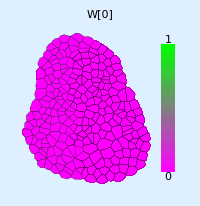

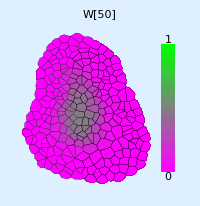

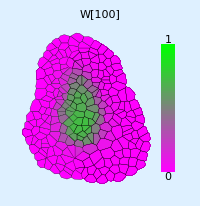

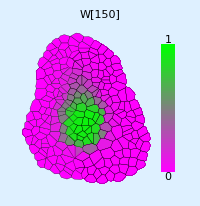

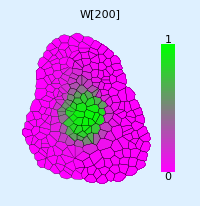

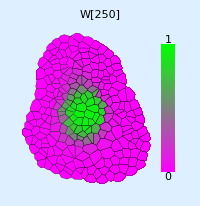

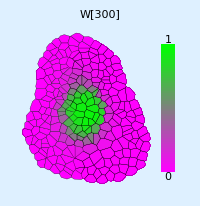

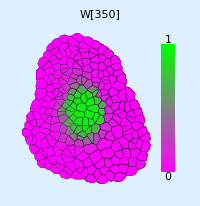

```mathematica
movieframes=animation[sim, {W, 0, 1}, {0, tmax, step}, cellCoordinates-> centers,RGBColors-> {{1,0,1},{0,1,0}}, cellNumbers-> False, wallThickness-> 0.001,Background-> LightBlue,ImageSize-> 200,TextStyle-> {FontFamily-> Times,FontSize-> 32}];
```

#### Optionally, look at the movie in Mathematica

```mathematica
ListAnimate[movieframes]
```

#### Save the movie to a separate file

Depending on which operating system you have, you can generate a movie. 
On linux, swf seems to work the fastest.
On macs, mov seems to be the best.
On Windows, avi seems to be the best. 

The value of $ExportFormats gives you a list of formats which Mathematica supports in your operating system, but it includes more than just movies. For example, on my linux system, the only movie formats are AVI, FLV, SWF. Most macs & pcs will probably have a lot more.

It is also possible to export each of the movie frames as a jpg or pdf or ps image and end then use a program like ffmpeg (on linux) or Quicktime Pro (on a mac) to generate a movie in any format.

```mathematica
Export["WUSCHEL-movie.swf", movieframes]
```

```mathematica
Export["WUSCHEL-movie.mov", movieframes]
```

```mathematica
Export["WUSCHEL-movie.avi", movieframes]
```